Example1: Vector Field 2D

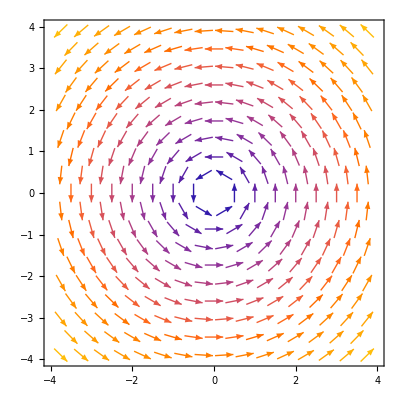

```mathematica
VectorPlot[{-y,x},{x,-4,4},{y,-4,4}]
```

The associated integral curves are shown below:

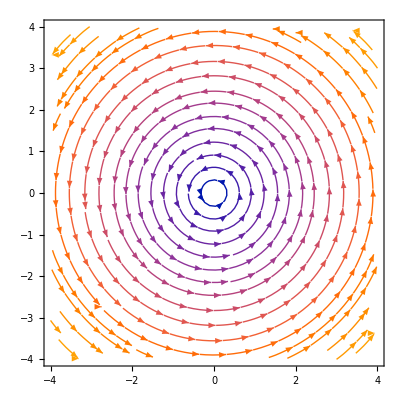

```mathematica
StreamPlot[{-y,x},{x,-4,4},{y,-4,4}]
```

Another vector field

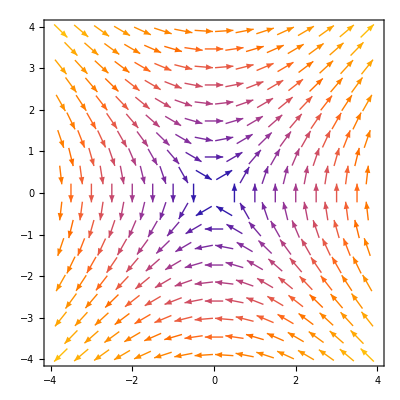

```mathematica
VectorPlot[{y,x},{x,-4,4},{y,-4,4}]
```

The associated integral curves are shown below:

```mathematica
StreamPlot[{y,x},{x,-4,4},{y,-4,4},StreamScale->None]
```

-Graphics-

Change of coordinate vector field under rotation

```mathematica
Animate[Show[VectorPlot[{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}},{x,-4,4},{y,-4,4},Axes->True,VectorColorFunction->None,VectorStyle->{Opacity[1,Red],Opacity[1,Blue]},VectorPoints->Coarse],VectorPlot[{{1,0},{0,1}},{x,-4,4},{y,-4,4},Axes->True,VectorColorFunction->None,VectorStyle->{Opacity[.3,Red],Opacity[.3,Blue]},VectorPoints->Coarse]],{t,0,2Pi}]
```

Example2: Vector field on a surface (taken from Mathematica documentation)

```mathematica
SliceVectorPlot3D[{y,-x,z}, {x^2-y^2-z==0},{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

Example3: Vector field on sphere (taken from Mathematica documentation)

```mathematica
SliceVectorPlot3D[{y,-x,z},"CenterSphere",{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
VectorPlot3D[{x,y,z},{x,y,z}∈Ball[]]
```

-Graphics3D-

Example4: vector field on Torus

Let us parameterize the torus

```mathematica
R = 4;
r = 2;
torus[u_,v_]={(r Cos[u]+R)Cos[v], (r Cos[u]+R)Sin[v], r Sin[u]};
```

```mathematica
ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},Mesh->None,PlotStyle->Texture[StreamPlot[{u+v,u-v},{u,0,2 Pi},{v,0,2 Pi},Frame->None,ImageSize->Large,PlotRangePadding->None]]]
```

-Graphics3D-